# FP Convergence Analysis

## Preliminaries

```mathematica
maindir=SetDirectory[NotebookDirectory[]]
nbf=NotebookFileName[]
```

/storage/disqs/CCxD/Analysis_SS

/storage/disqs/CCxD/Analysis_SS/FPConvergeAnalysis_SS.nb

### Setting Parameters

```mathematica
matrix = 0;
configs = 1000000000;
iditer = 9;
zrange = 25;
cropamt = 8;
bootstrapsets = 10;
project="CCGD";
importrange = Table[i,{i,0,(rgsteps = 20)}];
```

## Importing Data

```mathematica
datadir=maindir<>"/../"<>project<>"/data/";
SetDirectory[datadir];
filepath = datadir<>ToString[matrix]<>"-RG-"<>ToString[configs]<>"-"<>ToString[iditer]<>"/dists/";
zimport = Table[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[matrix]<>"-z"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,importrange}];
timport = Table[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[matrix]<>"-t"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,importrange}];
gimport = Table[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[matrix]<>"-g"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,importrange}];
croppedzimport = Table[Take[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[matrix]<>"-z"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{1000* (zrange -cropamt),1000*(zrange+cropamt)}],{i,importrange}];
```

## Normalizing and Plotting Data

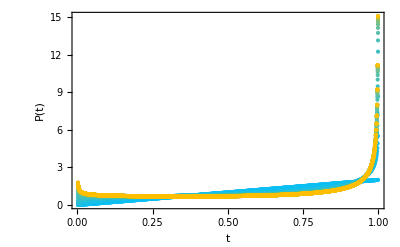

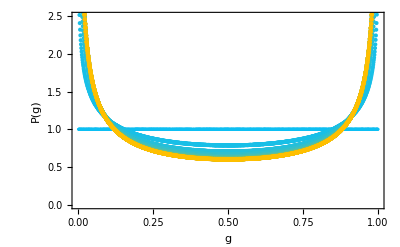

-Graphics-

-Graphics-

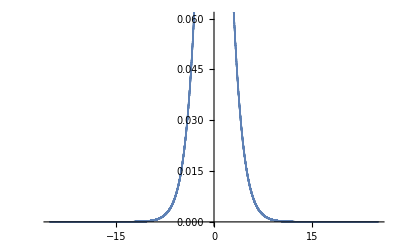

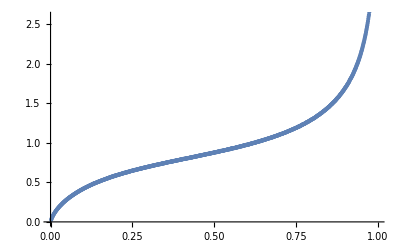

```mathematica
ttotal = Table[Total[ToExpression[Take[timport[[i]],{2,999}]]],{i,1,Length[importrange]}];
gtotal = Table[Total[ToExpression[Take[gimport[[i]],{2,999}]]],{i,1,Length[importrange]}];
ztotal = Table[Total[zimport[[i]]],{i,1,Length[importrange]}];
tnormalized = Table[{j/1000,1000*ToExpression[timport[[i]][[j]]]/ttotal[[i]]},{i,1,Length[importrange]},{j,2,Length[timport[[1]]]-1}];
gnormalized = Table[{j/1000,1000*ToExpression[gimport[[i]][[j]]]/gtotal[[i]]},{i,1,Length[importrange]},{j,2,Length[gimport[[1]]-1]}];
znormalized = Table[{(j/1000)-(zrange + 0.0005),1000*zimport[[i]][[j]]/ztotal[[i]]},{i,1,Length[importrange]},{j,1,Length[zimport[[1]]]}];
zcroppednormalized = Table[Take[znormalized[[i]],{1000* (zrange -cropamt),1000*(zrange+cropamt)}],{i,1,Length[importrange]}];

tplot=List[];
gplot = List[];
zplot = List[];
croppedzplot = List[];
For[i=1,i<=Length[importrange],i++,
(
AppendTo[tplot,ListPlot[tnormalized[[i]],PlotStyle->RGBColor[i/Length[importrange],0.75,1-(i/Length[importrange])]]];
AppendTo[gplot,ListPlot[gnormalized[[i]],PlotStyle->RGBColor[i/Length[importrange],0.75,1-(i/Length[importrange])]]];
AppendTo[zplot,ListPlot[znormalized[[i]],PlotStyle->RGBColor[i/Length[importrange],0.75,1-(i/Length[importrange])]]];
AppendTo[croppedzplot,ListPlot[zcroppednormalized[[i]],PlotStyle->RGBColor[i/Length[importrange],0.75,1-(i/(Length[importrange]))]]];
)];
Show[tplot, Frame->True,PlotRange->{{0,1},{0,Automatic}},LabelStyle->{FontSize->24}, FrameLabel->{t,"P(t)"}]
Show[gplot,Frame->True, PlotRange->{{0,1},{0,2.5}},LabelStyle->{FontSize->24},FrameLabel->{g,"P(g)"}]
Show[zplot,Frame->True,PlotRange->All,LabelStyle->{FontSize->24},FrameLabel->{z,"Q(z)"}]
Show[croppedzplot,Frame->True,PlotRange->{Automatic,{0,Automatic}},LabelStyle->{FontSize->24},FrameLabel->{z,"Q(z)"}]
ListPlot[znormalized[[2]]]
ListPlot[tnormalized[[2]]]
```

## Analysis

```mathematica
ex = Table[znormalized[[i]][[j]][[1]]*znormalized[[i]][[j]][[2]]*(1/1000),{i,1,Length[importrange]},{j,1,Length[znormalized[[1]]]}];
exsquared = Table[znormalized[[i]][[j]][[1]]^2*znormalized[[i]][[j]][[2]]*(1/1000),{i,1,Length[importrange]},{j,1,Length[znormalized[[1]]]}];
var = Table[Total[exsquared[[i]]]-Total[ex[[i]]]^2,{i,1,Length[importrange]}];
stdev = Table[Sqrt[var[[i]]],{i,1,Length[importrange]}];
difference = Table[Abs[znormalized[[i+1]][[j]][[2]]-znormalized[[i]][[j]][[2]]]^2,{i,1,Length[znormalized]-1},{j,1,Length[znormalized[[1]]]}];
delta = Table[Sqrt[(1/1000)*(Total[difference[[i]]])],{i,1,Length[znormalized]-1}];
```

#### Variance as a function of RG step

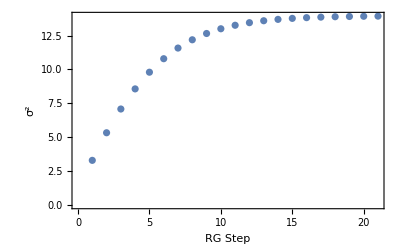

{3.28994,5.32665,7.07865,8.56298,9.79403,10.7904,11.5766,12.1873,12.6509,12.9996,13.2584,13.4493,13.5917,13.6928,13.7666,13.8201,13.8583,13.8879,13.9056,13.9216,13.9325}

```mathematica
ListPlot[var, Frame->True, LabelStyle->{FontSize->24},FrameLabel->{"RG Step",σ^2}]
var
```

#### Standard Deviation as a function of RG step

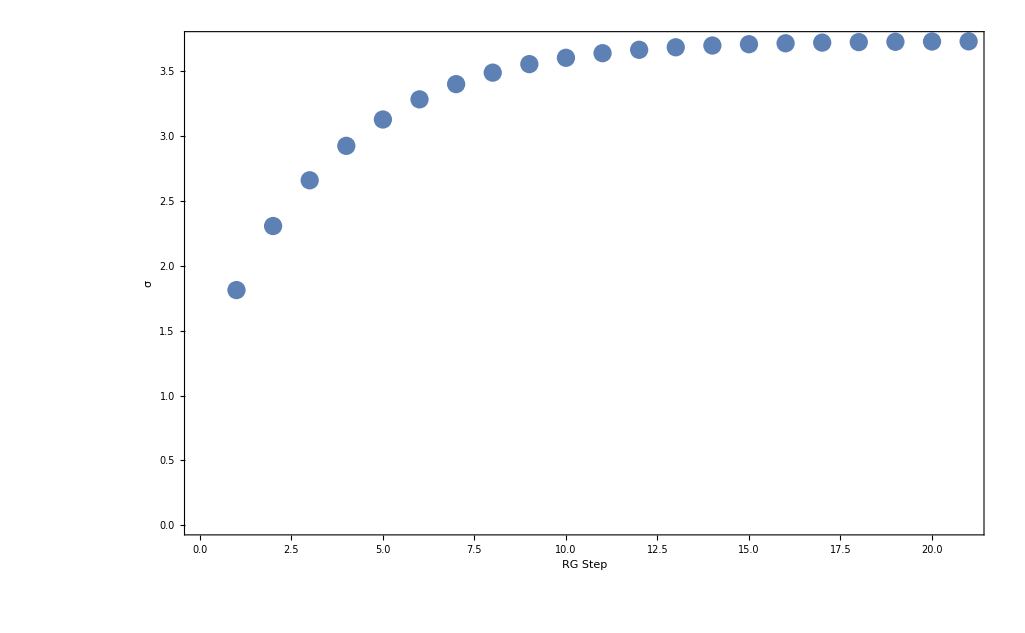

{1.81382,2.30795,2.66057,2.92626,3.12954,3.28488,3.40244,3.49103,3.55681,3.60549,3.64121,3.66733,3.68669,3.70037,3.71033,3.71754,3.72267,3.72665,3.72902,3.73116,3.73262}

```mathematica
ListPlot[stdev, Frame->True, LabelStyle->{FontSize->24},FrameLabel->{"RG Step","σ"}]
stdev
```

#### Difference between successive RG steps as a function of RG step

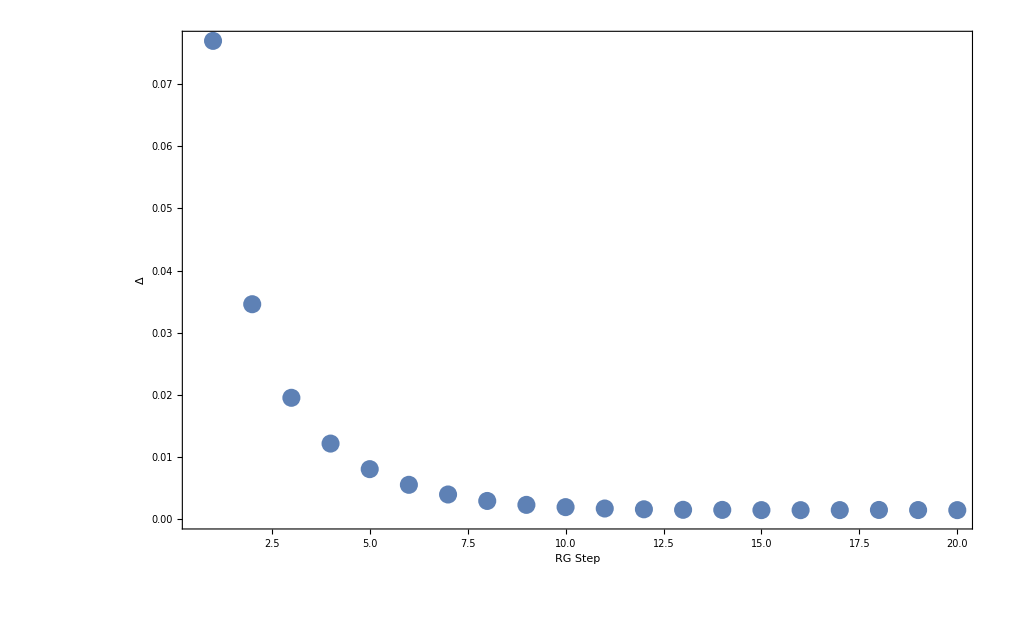

```mathematica
ListPlot[delta,Frame->True, LabelStyle->{FontSize->24},FrameLabel->{"RG Step","Δ"}, PlotRange->Full]
```

```mathematica
delta
```

{0.0769106,0.0345842,0.0195447,0.0121856,0.00807726,0.00555814,0.00400191,0.00296437,0.00233436,0.00197172,0.00175028,0.00162377,0.00154105,0.00152711,0.00149163,0.00148514,0.0014946,0.00151846,0.00150225,0.00148949}

## Saving

```mathematica
Directory[]
SetDirectory[maindir]
```

/storage/disqs/CCxD/CCGD/data

/storage/disqs/CCxD/Analysis_SS

```mathematica
nbf=NotebookFileName[]
NotebookSave[EvaluationNotebook[],"FPAnalysis-"<>ToString[project]<>"-"<>ToString[configs]<>"-"<>ToString[matrix]<>"-"<>DateString[{"Day","-","Month","-","Year"}]<>".nb"]
NotebookSave[EvaluationNotebook[],nbf]
```

/storage/disqs/CCxD/Analysis_SS/FPConvergeAnalysis_SS.nb